```mathematica
DateString[]
<<SymbolicComputing`
$Version
$SCVersion
```

Tue 16 May 2023 10:11:57

13.2.0 for Microsoft Windows (64-bit) (November 18, 2022)

6.0.2 (June 28, 2021)

## Lecture 16 edited by Chi-Ok Hwang, originally made by Dr. 전 경원

[1] C. Arangala, Exploring Linear Algebra: Labs and Projects with Mathematica ®, 1st ed. Boca Raton: Chapman and Hall/CRC, 2014.

-Graphics-

## 4 Orthogonality

## Lab 16: Inner Product Spaces

### Introduction

An inner product on set V is a function that maps ordered pairs (x,y) from V×V to a number ⟨x,y⟩ while satisfying the following properties:
1. ∀v⃗∈V,  ⟨v⃗,v⃗⟩≥0 and ⟨v⃗,v⃗⟩=0 iff v⃗=OverVector[0].
2. ∀u,v,w∈V, ⟨u,v+w⟩=⟨u,v⟩+⟨u,w⟩.
3. ∀u,v∈V and k∈ℤ, ⟨k u,v⟩=⟨u,k v⟩=k⟨u,v⟩.
4. ∀u,v∈V, ⟨u,v⟩=⟨v,u⟩.

A vector space with a defined inner product is called an inner product space.

The Euclidean inner product a.k.a dot product, in R^n is defined as
⟨u,v⟩=∑_(i=1)^n u_i v_i
where u=Table[u_i,{i,n}], v=Table[v_i,{i,n}] are in R^n.

Exercises:

a.

```mathematica
SCARA[⟨u,v⟩,⟨u_,v_⟩->u.v]
SCMAF[%,RA,{At[2],{u=={3,2},v=={2,0}}}]
```

⟨u,v⟩==u.v

⟨u,v⟩==6

b.

```mathematica
‖u‖==√⟨u,u⟩
SCMAF[%,RR,{At[2],{⟨u_,v_⟩->u.v,u=={3,2}}}]
```

‖u‖==√⟨u,u⟩

‖u‖==√13

HoldFormpaclet:ref/HoldForm[expr]
prints as the expression expr, with expr maintained in an unevaluated form.

```mathematica
HoldForm@‖u‖==Norm[u]
SCMAF[%,RR,{At[2],{u=={3,2}}}]
```

‖u‖==‖u‖

‖u‖==√13

c.

```mathematica
SCARA[{û,v̂,ŵ},OverHat[u_]==(u⃗)/(‖u⃗‖)]//Thread
SCMAF[%,RA,{At[All,2],{u⃗=={3,2},v⃗=={2,0},w⃗=={0,2}}}]
```

{û==(u⃗)/(‖u⃗‖),v̂==(v⃗)/(‖v⃗‖),ŵ==(w⃗)/(‖w⃗‖)}

{û=={3/(√13),2/(√13)},v̂=={1,0},ŵ=={0,1}}

```mathematica
{û,v̂,ŵ}==Normalize/@{u⃗,v⃗,w⃗}//Thread
SCMAF[%,RA,{At[All,2],{u⃗=={3,2},v⃗=={2,0},w⃗=={0,2}}}]
```

{û==(u⃗)/(‖u⃗‖),v̂==(v⃗)/(‖v⃗‖),ŵ==(w⃗)/(‖w⃗‖)}

{û=={3/(√13),2/(√13)},v̂=={1,0},ŵ=={0,1}}

d.

Difference between @@ and @@@

```mathematica
ClearAll["Global`*"]
f@@#& //FullForm
f@@{{a,b},{c,d},{e,i}}
ClearAll["Global`*"]
f@@@{{a,b},{c,d},{e,i}}
ClearAll["Global`*"]
f@@#&/@{{a,b} ,{c,d},{e,i}}
```

Function[Apply[f,Slot[1]]]

f[{a,b},{c,d},{e,i}]

{f[a,b],f[c,d],f[e,i]}

{f[a,b],f[c,d],f[e,i]}

Subsets | 
Subsetspaclet:ref/Subsets[list]
gives a list of all possible subsets of list. 
Subsetspaclet:ref/Subsets[list,n]
gives all subsets containing at most n elements. 
Subsetspaclet:ref/Subsets[list,{n}]
gives all subsets containing exactly n elements.

```mathematica
SCARA[Dot@@Subsets[{u⃗,v⃗,w⃗},{2}],{u⃗=={3,2},v⃗=={2,0},w⃗=={0,2}}]//Thread
```

{((u⃗)^2+v⃗ w⃗).{v⃗,w⃗}==18,((u⃗)^2+v⃗ w⃗).{v⃗,w⃗}==8}

```mathematica
SCARA[Dot@@@Subsets[{u⃗,v⃗,w⃗},{2}],{u⃗=={3,2},v⃗=={2,0},w⃗=={0,2}}]//Thread
```

{u⃗.v⃗==6,u⃗.w⃗==4,v⃗.w⃗==0}

### More about Orthogonality

A set is called orthogonal if ∀v≠w∈V and ⟨v,w⟩=0.

In addition, if ∀v∈V, ⟨v,v⟩=1 then the set is called orthonormal.

A basis for an orthonormal set is an orthonormal basis.

If V_1 is a subset of V, then th eorthogonal complement of V_1 is the set of all vectors in V that are orthogonal to every vector in V_1.

Exercises:

a.

```mathematica
SCUnitVecToVec[{x̂,ŷ,ẑ},{x̂,ŷ,ẑ}]
```

{{1,0,0},{0,1,0},{0,0,1}}

b.

Difference between Plus and Total

```mathematica
Plus[1,2,3]
Plus[{1,2,3}]
Total[{1,2,3}]
Total[1,2,3]
```

6

{1,2,3}

6

Total::nonopt: Options expected (instead of 3) beyond position 2 in Total[1,2,3]. An option must be a rule or a list of rules.

Total[1,2,3]

```mathematica
SCARA[⟨U,V⟩,{U==({{Subscript[u, 1], Subscript[u, 2]}, {Subscript[u, 3], Subscript[u, 4]}}),V==({{Subscript[v, 1], Subscript[v, 2]}, {Subscript[v, 3], Subscript[v, 4]}})}]
SCMAF[%,RA,{At[2],⟨U_,V_⟩:>Total[Flatten[U V]]}]
```

⟨U,V⟩==⟨{{u_1,u_2},{u_3,u_4}},{{v_1,v_2},{v_3,v_4}}⟩

⟨U,V⟩==u_1 v_1+u_2 v_2+u_3 v_3+u_4 v_4

```mathematica
SCARA[⟨#1,#2⟩&@@@Subsets[{U,V,W,X},{2}],{U==({{1, 0}, {0, 0}}),V==({{0, 1}, {0, 0}}),W==({{0, 0}, {1, 0}}),X==({{0, 0}, {0, 1}})}]
SCMAF[%,RA,{At[2],⟨U_,V_⟩:>Total[Flatten[U V]]},PostAll->Thread]
```

{⟨U,V⟩,⟨U,W⟩,⟨U,X⟩,⟨V,W⟩,⟨V,X⟩,⟨W,X⟩}=={⟨{{1,0},{0,0}},{{0,1},{0,0}}⟩,⟨{{1,0},{0,0}},{{0,0},{1,0}}⟩,⟨{{1,0},{0,0}},{{0,0},{0,1}}⟩,⟨{{0,1},{0,0}},{{0,0},{1,0}}⟩,⟨{{0,1},{0,0}},{{0,0},{0,1}}⟩,⟨{{0,0},{1,0}},{{0,0},{0,1}}⟩}

{⟨U,V⟩==0,⟨U,W⟩==0,⟨U,X⟩==0,⟨V,W⟩==0,⟨V,X⟩==0,⟨W,X⟩==0}

c.

Partitionpaclet:ref/Partition[list,n]
partitions list into nonoverlapping sublists of length n. 
Partitionpaclet:ref/Partition[list,n,d]
generates sublists with offset d. 
Partitionpaclet:ref/Partition[list,{n_1,n_2,…}]
partitions a nested list into blocks of size n_1×n_2×….

```mathematica
SCARA[NullSpace[A],A==Partition[Range[9],3]]
```

NullSpace[A]=={{1,-2,1}}

```mathematica
SCARA[RowReduce[A],A==Partition[Range[9],3]]
```

RowReduce[A]=={{1,0,-1},{0,1,2},{0,0,0}}

```mathematica
{1,-2,1}.#&/@{{1,0,-1},{0,1,2},{0,0,0}}
```

{0,0,0}

d.

```mathematica
SCARA[NullSpace[A^T],A==Partition[Range[9],3]]
```

NullSpace[A^T]=={{1,-2,1}}

```mathematica
c[A]=={{1,4,7},{2,5,8}};
```

```mathematica
{1,-2,1}.#&/@{{1,4,7},{2,5,8}}
```

{0,0}

### Gram-Schmidt Process

The Gram–Schmidt process is a method for orthonormalising a set of vectors in an inner product space.

The algorithm in ℝ^n
1. Start with n linearly independent vectors Table[v_i,{i,n}].
2. Let u_1=v_1 and e_1=u_1/(‖u_1‖).
3. Project v_2 onto e_1, proj_e_1[v_2]=⟨v_2,e_1⟩e_1.
4. Define u_2=v_2-proj_e_1[v_2] and e_2=u_2/(‖u_2‖).
5. In general u_n=v_n-∑_(i=1)^(n-1) proj_u_i[v_n] and e_n=u_n/(‖u_n‖).

### Instability of the Algorithm

Exercises:

a.

```mathematica
NullSpace[{{1,2,2},{4,5,6},{8,9,1}}]
Length@NullSpace[{{1,2,2},{4,5,6},{8,9,1}}]
```

{}

0

```mathematica
Clear[myGramSchmidt]
myGramSchmidt[v_/;MatrixQ@v]:=Module[{e={},u,n=1},
While[n≠Length[v]+1,
u=v[[n]]-Sum[(e[[i]].v[[n]])e[[i]],{i,1,n-1}];
AppendTo[e,u/Norm[u]];
n++];
e]
MatrixForm@myGramSchmidt[{{1,2,2},{4,5,6},{8,9,1}}]
```

(1/3 | 2/3 | 2/3
10/(3 √17) | -7/(3 √17) | 2/(3 √17)
2/(√17) | 2/(√17) | -3/(√17))

```mathematica
Dot@@@Subsets[{{1/3,2/3,2/3},{10/(3 √17),-7/(3 √17),2/(3 √17)},{2/(√17),2/(√17),-3/(√17)}},{2}]
```

{0,0,0}

Orthogonalizepaclet:ref/Orthogonalize[{v_1,v_2,…}] 
gives an orthonormal basis found by orthogonalizing the vectors v_i.

```mathematica
Table[Subscript[e, i],{i,3}]==Orthogonalize[{{1,2,2},{4,5,6},{8,9,1}}]//Thread
```

{e_1=={1/3,2/3,2/3},e_2=={10/(3 √17),-7/(3 √17),2/(3 √17)},e_3=={2/(√17),2/(√17),-3/(√17)}}

b.

```mathematica
Length@NullSpace[{{1.,10^-7,10^-7},{1,10^-7,0},{1,0,10^-7}}]
```

0

```mathematica
myGramSchmidt[{{1.,10^-7,10^-7},{1,10^-7,0},{1,0,10^-7}}]
Dot@@@Subsets[%,{2}]
```

{{1.,1.×10^-7,1.×10^-7},{9.99201×10^-8,9.92617×10^-15,-1.},{9.992×10^-8,-1.,-0.000799278}}

{-7.99278×10^-11,-1.59856×10^-10,0.000799278}

c.

```mathematica
Clear[myGramSchmidt]
myGramSchmidt[v_/;MatrixQ@v]:=Module[{e={},u,n=1},
While[n≠Length[v]+1,
u=v[[n]]-Sum[(e[[i]].v[[n]])e[[i]],{i,1,n-1}];
AppendTo[e,u/Norm[u]];
n++];
e]
MatrixForm@myGramSchmidt[{{1,2,2},{4,5,6},{8,9,1}}]
```

(1/3 | 2/3 | 2/3
10/(3 √17) | -7/(3 √17) | 2/(3 √17)
2/(√17) | 2/(√17) | -3/(√17))

```mathematica
myGramSchmidt[{{1.`20,10^-7,10^-7},{1,10^-7,0},{1,0,10^-7}}]
Dot@@@Subsets[%,{2}]//Chop
```

{{0.99999999999999,9.9999999999999×10^-8,9.9999999999999×10^-8},{1.×10^-7,1.×10^-14,-1.},{1.×10^-7,-1.,0.}}

{0,0,0.}

### Theorems and Problems

Theorem 60. If u and v are orthogonal vectors in V then
‖u+v‖=‖u‖+‖v‖.

It’s false. The following ix a counter example.

```mathematica
SCARA[u.v,{u=={1,0},v=={0,1}}]
```

u.v==0

```mathematica
Norm[u+v]==Norm[u]+Norm[v]
SCMAF[%,RA,{All,{u=={1,0},v=={0,1}}}]
```

‖u+v‖==‖u‖+‖v‖

False

Theorem 61. If u and v are vectors in V then
|⟨u,v⟩|≤‖u‖‖v‖.

It’s true.

Let θ is the angle between u⃗ and v⃗.

```mathematica
{|⟨u,v⟩|==‖u‖ ‖v‖ |Cos[θ]|,‖u‖ ‖v‖ |Cos[θ]|≤‖u‖‖v‖}
SCMAF[%,SCEliminate,{All,‖u‖ ‖v‖ |Cos[θ]|,1}]
```

{|⟨u,v⟩|==|Cos[θ]| ‖u‖ ‖v‖,|Cos[θ]| ‖u‖ ‖v‖≤‖u‖ ‖v‖}

|⟨u,v⟩|≤‖u‖ ‖v‖

Theorem 62. If u and v are vectors in V then 
|u+v|≤‖u‖‖v‖.

It’s true.

Let α is the angle between u⃗ and u⃗+v⃗. Also, let α is the angle between v⃗ and u⃗+v⃗.

◼ SCAddEqs[{eq_1, eq_2, …}] adds the left-hand sides and the right-hand sides of all equations separately.
◼ SCAddEqs[{eq_1, eq_2, …}, {i, j, …}] adds the left-hand sides and the right-hand sides of eq_i, eq_j, … separately and replaces eq_i with the result.

```mathematica
{‖u‖Cos[α]≤‖u‖,‖v‖Cos[β]≤‖v‖}
SCMAF[%,SCAddEqs,All,
SCEliminate,{All,‖u+v‖==‖u‖Cos[α]+‖v‖Cos[β],‖u‖Cos[α]+‖v‖Cos[β]}]
```

{Cos[α] ‖u‖≤‖u‖,Cos[β] ‖v‖≤‖v‖}

Cos[α] ‖u‖+Cos[β] ‖v‖≤‖u‖+‖v‖

‖u+v‖≤‖u‖+‖v‖

Problem 63. If u  and v are vectors in V then
(‖u+v‖)^2+(‖u-v‖)^2=2((‖u‖)^2+(‖v‖)^2).

Theorem 64. If  {v_1,v_2, …, v_n} is an orthonormal set of vectors in V, then
(‖k_1 v_1+k_2 v_2+ … +k_n v_n‖)^2=(|k_1|)^2+(|k_2|)^2+ … +(|k_n|)^2.

Theorem 65. Every orthonormal set of vectors is linearly independent.

Problem 66. If T:R^n→R^n is the linear transformation defined by left multiplication of the n×n matrix A and vector v is in the range of T then v is orthogonal to the nullspace of A.

## Lab 17: The Geometry of Vector and Inner Product Spaces

### Triangle Inequality

If V=ℝ^2 with the Euclidean inner product,

Demonstration: Sum of Two Vectors

Exercises:

a.

```mathematica
{‖u‖Cos[α]≤‖u‖,‖v‖Cos[β]≤‖v‖}
SCMAF[%,SCAddEqs,All,
SCEliminate,{All,‖u+v‖==‖u‖Cos[α]+‖v‖Cos[β],‖u‖Cos[α]+‖v‖Cos[β]}]
```

{Cos[α] ‖u‖≤‖u‖,Cos[β] ‖v‖≤‖v‖}

Cos[α] ‖u‖+Cos[β] ‖v‖≤‖u‖+‖v‖

‖u+v‖≤‖u‖+‖v‖

b.

```mathematica
Norm[u]+Norm[v]==Norm[u+v]
SCMAF[%,RA,{All,{u=={Subscript[u, 1],Subscript[u, 2]},v==c{Subscript[u, 1],Subscript[u, 2]}}},
Simplify,{All,c≥0}]
```

‖u‖+‖v‖==‖u+v‖

√((|u_1|)^2+(|u_2|)^2)+√((|c u_1|)^2+(|c u_2|)^2)==√((|u_1+c u_1|)^2+(|u_2+c u_2|)^2)

True

c.

```mathematica
SCARA[‖f[x]‖,‖f_‖==⟨f,f⟩]
SCMAF[%,RR,{At[2],{⟨f_,g_⟩->∫_-1^1 f gⅆx,f[x]==x^2}},Post->SCEvalInt]
```

‖f[x]‖==⟨f[x],f[x]⟩

‖f[x]‖==2/5

```mathematica
SCARA[‖g[x]‖,‖f_‖==⟨f,f⟩]
SCMAF[%,RR,{At[2],{⟨f_,g_⟩->∫_-1^1 f gⅆx,g[x]==x}},Post->SCEvalInt]
```

‖g[x]‖==⟨g[x],g[x]⟩

‖g[x]‖==2/3

```mathematica
SCARA[‖f[x]+g[x]‖,‖f_‖==⟨f,f⟩]
SCMAF[%,RR,{At[2],{⟨f_,g_⟩->∫_-1^1 f gⅆx,f[x]==x^2,g[x]==x}},Post->SCEvalInt]
```

‖f[x]+g[x]‖==⟨f[x]+g[x],f[x]+g[x]⟩

‖f[x]+g[x]‖==16/15

d.

Demonstration: Triangle Inequality for Functions

```mathematica
‖f[x]+g[x]‖≤‖f[x]‖+‖g[x]‖
SCMAF[%,RA,{All,{‖f[x]‖==2/5,‖g[x]‖==2/3,‖f[x]+g[x]‖==16/15}}]
```

‖f[x]+g[x]‖≤‖f[x]‖+‖g[x]‖

True

### Cauchy-Schwarz Inequality

Exercises:

a.

Demonstration: The Cauchy-Schwarz Inequality for Vectors in the Plane

b.

```mathematica
‖u‖‖v‖==|⟨u,v⟩|
SCMAF[%,RA,{At[2],⟨u,v⟩==‖u‖‖v‖Cos[θ]},
SCSolve,{All,θ}]
```

‖u‖ ‖v‖==|⟨u,v⟩|

‖u‖ ‖v‖==|Cos[θ]| ‖u‖ ‖v‖

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

SCMAF::stopped: Stopped due to error.

{{θ==0},{θ==-π},{θ==π}}

c.

```mathematica
SCARR[‖f‖‖g‖,{‖f_‖->⟨f,f⟩,⟨f_,g_⟩->∫_-1^1 f gⅆx}]
SCMAF[%,SCRestoreFunc,{At[2],{f,g},Variables->x},
RA,{At[2],{f[x]==x^2,g[x]==x}},Post->SCEvalInt]
```

‖f‖ ‖g‖==(∫_-1^1 f^2 ⅆx)∫_-1^1 g^2 ⅆx

‖f‖ ‖g‖==(∫_-1^1 f[x]^2 ⅆx)∫_-1^1 g[x]^2 ⅆx

‖f‖ ‖g‖==4/15

```mathematica
SCARA[|⟨f,g⟩|,{⟨f_,g_⟩->∫_-1^1 f gⅆx}]
SCMAF[%,SCRestoreFunc,{At[2],{f,g},Variables->x},
RA,{At[2],{f[x]==x^2,g[x]==x}},Post->SCEvalInt]
```

|⟨f,g⟩|==|∫_-1^1 f gⅆx|

|⟨f,g⟩|==|∫_-1^1 f[x] g[x]ⅆx|

|⟨f,g⟩|==0

```mathematica
‖f‖ ‖g‖>|⟨f,g⟩|
SCMAF[%,RA,{All,{‖f‖ ‖g‖==4/15,|⟨f,g⟩|==0}}]
```

‖f‖ ‖g‖>|⟨f,g⟩|

True

d.

Demonstration: Cauchy-Schwarz Inequality for Integrals

### Change of Coordinates of a Vector

Exercises:

a.

```mathematica
({{1}, {2}})==({{1, 0}, {0, 1}}).({{Subscript[c, 1]}, {Subscript[c, 2]}})
SCMAF[%,SCSolve,{All,{Subscript[c, 1],Subscript[c, 2]}}]
```

{{1},{2}}=={{c_1},{c_2}}

{c_1==1,c_2==2}

```mathematica
({{-1}, {2}})==({{1, 0}, {0, 1}}).({{Subscript[c, 3]}, {Subscript[c, 4]}})
SCMAF[%,SCSolve,{All,{Subscript[c, 3],Subscript[c, 4]}}]
```

{{-1},{2}}=={{c_3},{c_4}}

{c_3==-1,c_4==2}

```mathematica
Subscript[P, 1]==({{Subscript[c, 1], Subscript[c, 3]}, {Subscript[c, 2], Subscript[c, 4]}})
SCMAF[%,RA,{All,Join[{Subscript[c, 1]==1,Subscript[c, 2]==2},{Subscript[c, 3]==-1,Subscript[c, 4]==2}]},MatrixForm->True]
```

P_1=={{c_1,c_3},{c_2,c_4}}

P_1==(1 | -1
2 | 2)

Khan Academy: Change of basis matrix

b.

```mathematica
Subscript[P, 1].({{1}, {-1}})/.Subscript[P, 1]->({{1, -1}, {2, 2}})//MatrixForm
```

(2
0)

c.

```mathematica
({{1}, {2}})==({{1, -1}, {2, 2}}).({{Subscript[c, 1]}, {Subscript[c, 2]}})
SCMAF[%,SCSolve,{All,{Subscript[c, 1],Subscript[c, 2]}}]
```

{{1},{2}}=={{c_1-c_2},{2 c_1+2 c_2}}

{c_1==1,c_2==0}

```mathematica
({{-2}, {1}})==({{1, -1}, {2, 2}}).({{Subscript[c, 3]}, {Subscript[c, 4]}})
SCMAF[%,SCSolve,{All,{Subscript[c, 3],Subscript[c, 4]}}]
```

{{-2},{1}}=={{c_3-c_4},{2 c_3+2 c_4}}

{c_3==-3/4,c_4==5/4}

```mathematica
Subscript[P, 2]==({{Subscript[c, 1], Subscript[c, 3]}, {Subscript[c, 2], Subscript[c, 4]}})
SCMAF[%,RA,{All,Join[{Subscript[c, 1]==1,Subscript[c, 2]==0},{Subscript[c, 3]==-3/4,Subscript[c, 4]==5/4}]},MatrixForm->True]
```

P_2=={{c_1,c_3},{c_2,c_4}}

P_2==(1 | -3/4
0 | 5/4)

```mathematica
Subscript[P, 2].Subscript[P, 1].({{1}, {-1}})/.{Subscript[P, 1]->({{1, -1}, {2, 2}}),Subscript[P, 2]->({{1, -3/4}, {0, 5/4}})}//MatrixForm
```

(2
0)

Demonstration: Coordinates of a Point Relative to a Basis in 2D

d.

## Lab 18: Orthogonal Matrices, QR Decomposition, and Least Squares Regression

### Introduction

An orthogonal matrix is a square matrix whose columns are orthogonal unit vectors.

Exercises:

a.

Three matrices are all orthogonal.

Practice

```mathematica
({{1, 2}, {3, 4}})[[2,2]]
```

4

```mathematica
A==({{1, 0}, {0, 1}})
SCMAF[%,#[[All,1]].#[[All,2]]&,At[2],Part->2]
```

A=={{1,0},{0,1}}

0

```mathematica
B==({{1/2, (√3)/2}, {(-√3)/2, 1/2}})
SCMAF[%,Transpose,All,Level->{1},MatrixForm->True,
Dot@@#&,At[2],Part->{2}]
```

B=={{1/2,(√3)/2},{-(√3)/2,1/2}}

B^T==(1/2 | -(√3)/2
(√3)/2 | 1/2)

0

```mathematica
M==({{1, 2}, {-2, 1}})
SCMAF[%,Transpose,All,Level->{1},MatrixForm->True,
Post,{Dot,At[2]},MainArg->2,Part->2]
```

M=={{1,2},{-2,1}}

M^T==(1 | -2
2 | 1)

Post[Dot,(1 | -2
2 | 1)]

A and B are normalized, while M is not.

```mathematica
A==({{1, 0}, {0, 1}})
SCMAF[%,Norm/@{#[[All,1]],#[[All,2]]}&,At[2],Part->2]
```

A=={{1,0},{0,1}}

{1,1}

```mathematica
B==({{1/2, (√3)/2}, {(-√3)/2, 1/2}})
SCMAF[%,Transpose,All,Level->{1},
Norm/@#&,At[2],Part->2]
```

B=={{1/2,(√3)/2},{-(√3)/2,1/2}}

B^T=={{1/2,-(√3)/2},{(√3)/2,1/2}}

{1,1}

```mathematica
M==({{1, 2}, {-2, 1}})
SCMAF[%,Transpose,All,Level->{1},
Map,{Norm,At[2]},MainArg->2,Part->2]
```

M=={{1,2},{-2,1}}

M^T=={{1,-2},{2,1}}

{√5,√5}

b.

```mathematica
A==({{1, 0}, {0, 1}})
SCMAF[%,Det,All,Level->{1}]
```

A=={{1,0},{0,1}}

Det[A]==1

```mathematica
B==({{1/2, (√3)/2}, {(-√3)/2, 1/2}})
SCMAF[%,Det,All,Level->{1}]
```

B=={{1/2,(√3)/2},{-(√3)/2,1/2}}

Det[B]==1

```mathematica
M==({{1, 2}, {-2, 1}})
SCMAF[%,Det,All,Level->{1}]
```

M=={{1,2},{-2,1}}

Det[M]==5

### QR Decomposition of Matrices

Exercises:

A QR decomposition of a matrix is a decomposition of a matrix A into a product A = Q.R of an orthogonal matrix Q and an upper triangular matrix R.

a.

```mathematica
Clear[myGramSchmidt]
Clear[myQRDecomposition]
myGramSchmidt[v_/;MatrixQ@v]:=Module[{e={},u,n=1},
While[n≠Length[v]+1,
u=v[[n]]-Sum[(e[[i]].v[[n]])e[[i]],{i,1,n-1}];
AppendTo[e,u/Norm[u]];
n++];
e]
myQRDecomposition[v_/;MatrixQ@v]:=Module[{n=1,a=Transpose[v],q,r},
q=myGramSchmidt[a];
r=Simplify@Table[If[i≤j,q[[i]].a[[j]],0],{i,Length[v]},{j,Length[a]}];
{q,r}]
MatrixForm/@myQRDecomposition[({{1, 4, 8}, {2, 5, 9}, {2, 6, 1}})]
```

{(1/3 | 2/3 | 2/3
10/(3 √17) | -7/(3 √17) | 2/(3 √17)
2/(√17) | 2/(√17) | -3/(√17)),(3 | 26/3 | 28/3
0 | (√17)/3 | 19/(3 √17)
0 | 0 | 31/(√17))}

b.

```mathematica
({{1/3, 2/3, 2/3}, {10/(3 √17), -7/(3 √17), 2/(3 √17)}, {2/(√17), 2/(√17), -3/(√17)}})//FullForm
Transpose[%]
```

List[List[Rational[1,3],Rational[2,3],Rational[2,3]],List[Times[Rational[10,3],Power[17,Rational[-1,2]]],Times[Rational[-7,3],Power[17,Rational[-1,2]]],Times[Rational[2,3],Power[17,Rational[-1,2]]]],List[Times[2,Power[17,Rational[-1,2]]],Times[2,Power[17,Rational[-1,2]]],Times[-3,Power[17,Rational[-1,2]]]]]

{{1/3,10/(3 √17),2/(√17)},{2/3,-7/(3 √17),2/(√17)},{2/3,2/(3 √17),-3/(√17)}}

```mathematica
Transpose[({{1/3, 2/3, 2/3}, {10/(3 √17), -7/(3 √17), 2/(3 √17)}, {2/(√17), 2/(√17), -3/(√17)}})]//FullForm
```

Syntax::bktmcp: Expression "Transpose[(1/3 | 2/3 | 2/3
10/(3 √17) | -7/(3 √17) | 2/(3 √17)
2/(√17) | 2/(√17) | -3/(√17))]//FullForm" has no closing "]".

```mathematica
SCARA[QRDecomposition[A],A==({{1, 4, 8}, {2, 5, 9}, {2, 6, 1}}),MatrixForm->True]
```

QRDecomposition[A]=={(1/3 | 2/3 | 2/3
10/(3 √17) | -7/(3 √17) | 2/(3 √17)
2/(√17) | 2/(√17) | -3/(√17)),(3 | 26/3 | 28/3
0 | (√17)/3 | 2/(3 √17)+(√17)/3
0 | 0 | 31/(√17))}

```mathematica
SCARA[Q.R,{Q==Transpose[({{1/3, 2/3, 2/3}, {10/(3 √17), -7/(3 √17), 2/(3 √17)}, {2/(√17), 2/(√17), -3/(√17)}})],R==({{3, 26/3, 28/3}, {0, (√17)/3, 2/(3 √17)+(√17)/3}, {0, 0, 31/(√17)}})},Post->Simplify,MatrixForm->True]
```

Q.R==(1 | 4 | 8
2 | 5 | 9
2 | 6 | 1)

QR decomposition of (1 | 2 | 3
4 | 5 | 6).

```mathematica
SCARA[QRDecomposition[A],A==({{1, 2, 3}, {4, 5, 6}}),MatrixForm->True]
```

QRDecomposition[A]=={(1/(√17) | 4/(√17)
4/(√17) | -1/(√17)),(√17 | 22/(√17) | 27/(√17)
0 | 3/(√17) | 6/(√17))}

```mathematica
SCARA[Q.R,{Q==Transpose[({{1/(√17), 4/(√17)}, {4/(√17), -1/(√17)}})],R==({{√17, 22/(√17), 27/(√17)}, {0, 3/(√17), 6/(√17)}})},MatrixForm->True]
```

Q.R==(1 | 2 | 3
4 | 5 | 6)

### Application to Linear Regression

Demonstration: Least Squares Criteria for the Least Squares Regression Line

Exercises:

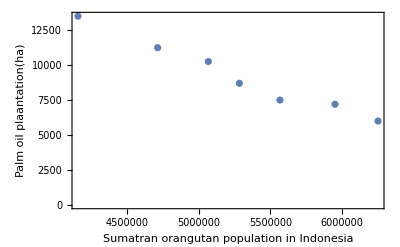

```mathematica
Block[{plantation,population},
plantation={4158077,4713431,5067058,5283557,5566635,5950349,6250460};
population={13500,11245,10254,8700,7500,7200,6000};
ListPlot[Thread@{plantation,population},Frame->True,FrameLabel->{"Sumatran orangutan population in Indonesia","Palm oil plaantation(ha)"}]
]
```

b.

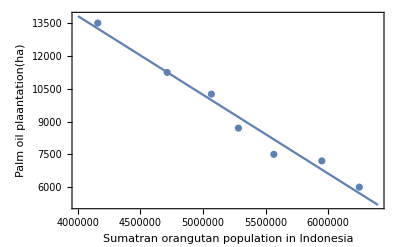

```mathematica
Block[{plantation,population,aa,bb,q,r,b,a},
plantation={4158077,4713431,5067058,5283557,5566635,5950349,6250460};
population={13500,11245,10254,8700,7500,7200,6000};
aa=Thread@{Table[1,Length@plantation],plantation};
bb=Transpose@{population};
{q,r}=QRDecomposition[aa];
{b,a}=Inverse[r].q.bb;
Show[
Plot[a x+b,{x,4 10^6,6.4 10^6}],
ListPlot[Thread@{plantation,population}],
PlotRange->All,Frame->True,FrameLabel->{"Sumatran orangutan population in Indonesia","Palm oil plaantation(ha)"}]
]
```

### Least Squares Regression Take 2

Exercises:

a, b.

```mathematica
Block[{plantation,population,aa,bb,a,b},
plantation={4158077,4713431,5067058,5283557,5566635,5950349,6250460};
population={13500,11245,10254,8700,7500,7200,6000};
aa=Thread@{Table[1,Length@plantation],plantation};
bb=Transpose@{population};
{b,a}=Inverse[Transpose[aa].aa].Transpose[aa].bb;
Show[
Plot[a x+b,{x,4 10^6,6.4 10^6}],
ListPlot[Thread@{plantation,population}],
PlotRange->All,Frame->True,FrameLabel->{"Sumatran orangutan population in Indonesia","Palm oil plaantation(ha)"}]
]
```

-Graphics-

c.

### Theorems and Problems

Problem 67. If A is an orthogonal square matrix then A^T=A^-1.

Problem 68. If A is an orthogonal square matrix then |A|=1.

## Lab 19: Symmetric Matrices and Quadratic Forms

### Introduction

Exercises:

a.

All eigenvectors are linearly independent. Therefore, A is diagonalizable.

```mathematica
SCARA[Eigenvectors[A],A==({{3, 2, -1}, {2, 3, -1}, {-1, -1, 4}})]
SCMAF[%,RowReduce,All,Level->{1}]
```

Eigenvectors[A]=={{-1,-1,1},{1,1,2},{-1,1,0}}

RowReduce[Eigenvectors[A]]=={{1,0,0},{0,1,0},{0,0,1}}

```mathematica
D==Inverse[P].A.P
SCMAF[%,RA,{At[2],{A==({{3, 2, -1}, {2, 3, -1}, {-1, -1, 4}}),P==Transpose[{{-1,-1,1},{1,1,2},{-1,1,0}}]}},MatrixForm->True]
```

D==P^-1.A.P

D==(6 | 0 | 0
0 | 3 | 0
0 | 0 | 1)

b.

f@@@expr or Applypaclet:ref/Apply[f,expr,{1}]
replaces heads at level 1 of expr by f.

```mathematica
Subsets[{{-1,-1,1},{1,1,2},{-1,1,0}},{2}]
```

{{{-1,-1,1},{1,1,2}},{{-1,-1,1},{-1,1,0}},{{1,1,2},{-1,1,0}}}

```mathematica
Dot@@@Subsets[{{-1,-1,1},{1,1,2},{-1,1,0}},{2}]
```

{0,0,0}

c.

```mathematica
Normalize/@{{-1,-1,1},{1,1,2},{-1,1,0}}
```

{{-1/(√3),-1/(√3),1/(√3)},{1/(√6),1/(√6),√(2/3)},{-1/(√2),1/(√2),0}}

```mathematica
D==Transpose[P].A.P
SCMAF[%,RA,{At[2],{A==({{3, 2, -1}, {2, 3, -1}, {-1, -1, 4}}),P==Transpose[{{-1/(√3),-1/(√3),1/(√3)},{1/(√6),1/(√6),√(2/3)},{-1/(√2),1/(√2),0}}]}},Post->Simplify,MatrixForm->True]
```

D==P^T.A.P

D==(6 | 0 | 0
0 | 3 | 0
0 | 0 | 1)

### Quadratic Forms

Exercises:

a.

Q_A is not bilinear.

```mathematica
Subscript[Q, A][u+v,w]==Subscript[Q, A][u,w]+Subscript[Q, A][v,w]
SCMAF[%,RA,{All,Subscript[Q, A][x1_,x2_]->x1^2+2x1 x2+x2^2},Post->FullSimplify]
```

Q_A[u+v,w]==Q_A[u,w]+Q_A[v,w]

2 u v==w^2

```mathematica
Subscript[Q, A][k v,w]==k Subscript[Q, A][u,w]
SCMAF[%,RA,{All,Subscript[Q, A][x1_,x2_]->x1^2+2x1 x2+x2^2},Post->FullSimplify]
```

Q_A[k v,w]==k Q_A[u,w]

(k v+w)^2==k (u+w)^2

b.

```mathematica
Subscript[Q, A][Subscript[x, 1],Subscript[x, 2]]==Transpose[x].A.x
SCMAF[%,RA,{At[2],{x==({{Subscript[x, 1]}, {Subscript[x, 2]}}),A==({{1, 1}, {1, 1}})}},Post->ExpandAll]
```

Q_A[x_1,x_2]==x^T.A.x

Q_A[x_1,x_2]=={{x_1^2+2 x_1 x_2+x_2^2}}

### Change of Variables in Quadratic Forms

Exercises:

a.

```mathematica
Subscript[Q, A][x]==Transpose[x].A.x
SCMAF[%,RA,{At[2],{x==({{Subscript[x, 1]}, {Subscript[x, 2]}, {Subscript[x, 3]}}),A==({{3, 2, -1}, {2, 3, -1}, {-1, -1, 4}})}},Post->ExpandAll]
```

Q_A[x]==x^T.A.x

Q_A[x]=={{3 x_1^2+4 x_1 x_2+3 x_2^2-2 x_1 x_3-2 x_2 x_3+4 x_3^2}}

b.

```mathematica
SCARA[Eigenvectors[A],A==({{3, 2, -1}, {2, 3, -1}, {-1, -1, 4}})]
```

Eigenvectors[A]=={{-1,-1,1},{1,1,2},{-1,1,0}}

```mathematica
Normalize/@{{-1,-1,1},{1,1,2},{-1,1,0}}//MatrixForm
```

(-1/(√3) | -1/(√3) | 1/(√3)
1/(√6) | 1/(√6) | √(2/3)
-1/(√2) | 1/(√2) | 0)

```mathematica
D==Transpose[P].A.P
SCMAF[%,RA,{At[2],{P==Transpose[({{-1/(√3), -1/(√3), 1/(√3)}, {1/(√6), 1/(√6), √(2/3)}, {-1/(√2), 1/(√2), 0}})],A==({{3, 2, -1}, {2, 3, -1}, {-1, -1, 4}})}},Post->Simplify,MatrixForm->True]
```

D==P^T.A.P

D==(6 | 0 | 0
0 | 3 | 0
0 | 0 | 1)

```mathematica
Subscript[Q, A][y]==Transpose[y].Transpose[P].A.P.y
SCMAF[%,RA,{At[2],Transpose[P].A.P==D},
RA,{At[2],{y==({{Subscript[y, 1]}, {Subscript[y, 2]}, {Subscript[y, 3]}}),D==({{6, 0, 0}, {0, 3, 0}, {0, 0, 1}})}},Post->ExpandAll]
```

Q_A[y]==y^T.P^T.A.P.y

Q_A[y]==y^T.D.y

Q_A[y]=={{6 y_1^2+3 y_2^2+y_3^2}}

c.

```mathematica
SCARA[Eigenvectors[A],A==({{1, 1}, {1, 1}})]
```

Eigenvectors[A]=={{1,1},{-1,1}}

```mathematica
Normalize/@{{1,1},{-1,1}}//MatrixForm
```

(1/(√2) | 1/(√2)
-1/(√2) | 1/(√2))

```mathematica
D==Transpose[P].A.P
SCMAF[%,RA,{At[2],{P==Transpose[({{1/(√2), 1/(√2)}, {-1/(√2), 1/(√2)}})],A==({{1, 1}, {1, 1}})}},Post->Simplify,MatrixForm->True]
```

D==P^T.A.P

D==(2 | 0
0 | 0)

```mathematica
Subscript[Q, A][y]==Transpose[y].Transpose[P].A.P.y
SCMAF[%,RA,{At[2],Transpose[P].A.P==D},
RA,{At[2],{y==({{Subscript[y, 1]}, {Subscript[y, 2]}}),D==({{2, 0}, {0, 0}})}},Post->ExpandAll]
```

Q_A[y]==y^T.P^T.A.P.y

Q_A[y]==y^T.D.y

Q_A[y]=={{2 y_1^2}}

d.

### Principal Axes Theorem

Example:

```mathematica
SCARA[Eigensystem[A],A==({{3, -2}, {-2, 3}})]
```

Eigensystem[A]=={{5,1},{{-1,1},{1,1}}}

```mathematica
Normalize/@{{-1,1},{1,1}}//MatrixForm
```

(-1/(√2) | 1/(√2)
1/(√2) | 1/(√2))

```mathematica
D==Transpose[P].A.P
SCMAF[%,RA,{At[2],{P==Transpose@({{-1/(√2), 1/(√2)}, {1/(√2), 1/(√2)}}),A==({{3, -2}, {-2, 3}})}},Post->Simplify,MatrixForm->True]
```

D==P^T.A.P

D==(5 | 0
0 | 1)

```mathematica
Subscript[Q, A][y]==Transpose[y].D.y
SCMAF[%,RA,{At[2],{y==({{Subscript[y, 1]}, {Subscript[y, 2]}}),D==({{5, 0}, {0, 1}})}}]
```

Q_A[y]==y^T.D.y

Q_A[y]=={{5 y_1^2+y_2^2}}

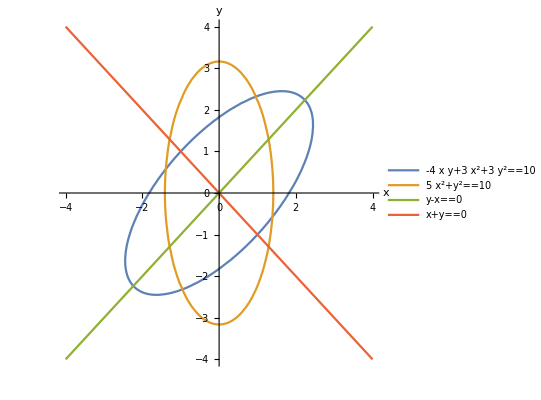

```mathematica
ContourPlot[{3 x^2-4x y+3 y^2==10,5 x^2+y^2==10,y-x==0,y+x==0},{x,-4,4},{y,-4,4},Axes->True,Frame->False,AxesLabel->Automatic,PlotLegends->"Expressions"]
```

### Properties of Quadratic Forms

Exercises:

a.

```mathematica
Subscript[Q, A][x]==Transpose[x].A.x
SCMAF[%,RA,{At[2],{x==({{Subscript[x, 1]}, {Subscript[x, 2]}}),A==({{1, 0}, {0, 1}})}}]
```

Q_A[x]==x^T.A.x

Q_A[x]=={{x_1^2+x_2^2}}

b.

```mathematica
Subscript[Q, A][x]==Transpose[x].A.x
SCMAF[%,RA,{At[2],{x==({{Subscript[x, 1]}, {Subscript[x, 2]}}),A==({{-1, 0}, {0, -1}})}}]
```

Q_A[x]==x^T.A.x

Q_A[x]=={{-x_1^2-x_2^2}}

c.

```mathematica
SCARA[Eigenvalues[A],A==({{1, 2}, {2, 1}})]
```

Eigenvalues[A]=={3,-1}

```mathematica
SCARA[Eigenvalues[A],A==({{-1, 0}, {0, -1}})]
```

Eigenvalues[A]=={-1,-1}

Exercises:

a.

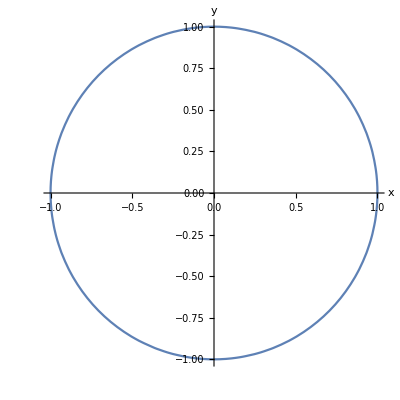

```mathematica
ContourPlot[x^2+y^2==1,{x,-1,1},{y,-1,1},Frame->False,Axes->True,AxesLabel->Automatic]
```

b.

Demonstration: Conic Sections: Equations and Graphs

c.

d.

e.

### Theorems and Problems

Theorem 69. If A is symmetric then any two eigenvectors of A are orthogonal.

Theorem 70. If A is symmetric then A is orthogonally diagonalizable.

Problem 71. If Q(x_1,x_2,x_3, …, x_n) is a quadratic form with all real coefficients then it is positive definite iff
Q(x_1,x_2,x_3,…,x_n)=x_1^2+x_2^2+x_3^2+…+x_n^2.

Theorem 72. A quadratic form Q is positive definite iff the eigenvalues of the coefficient matrix A are all positive.

Theorem 73. If A is a positive or negative definite matrix then A is invertible.

Problem 74. If A is a symmetric 2×2 matrix with eigenvalues λ_1≥λ_2 and Q_A is the quadratic form defined by Q_A(x)=x^T A x, then the conic section defined by Q_A(x)=1 is
(1) an ellipse if λ_1≥λ_2>0.
(2) a hyperbola if λ_1>0>λ_2,
(3) the empty set if 0≥λ_1≥_2 and
(4) two parallel lines if λ_1>λ_2=0.

```mathematica
SCTransInt[∫_(-∞)^∞ f[x]ⅆx,TransVar->{x,θ,θ==ArcTan[x]},Post->Simplify]
```

∫_(-π/2)^(π/2) f[Tan[θ]] Sec[θ]^2ⅆθ

```mathematica
SCEvalInt[∫_1^2 1/(3-5 x)^2 ⅆx]
```

1/14

```mathematica
SCTransInt[∫_1^2 1/(3-5 x)^2 ⅆx,TransVar->{x,u,u==3-5x},Post->Simplify]
```

∫_-7^-2 1/(5 u^2)ⅆu

```mathematica
∫_-7^-2 1/(5 u^2)ⅆu
SCEvalInt[%]
```

∫_-7^-2 1/(5 u^2)ⅆu

1/14

```mathematica
∫_1^2 1/(3-5 x)^2 ⅆx;
SCAFE[%,SCTransInt,{All,TransVar->{x,u,u==3-5x}},SCEvalInt,{At[2]}]
```

∫_1^2 1/(3-5 x)^2 ⅆx==1/5 ∫_-7^-2 1/u^2 ⅆu

∫_1^2 1/(3-5 x)^2 ⅆx==1/14